```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2 Kb

{Utilities`CleanSlate`,System`,Global`}

```mathematica
Clear[q]
q = { x[t], θ[t] }
```

{x[t],θ[t]}

```mathematica
Clear[r]
r = { x[t] + a Sin[θ[t]] , -a Cos[θ[t]] }
```

{a Sin[θ[t]]+x[t],-a Cos[θ[t]]}

```mathematica
D[r, t]
```

{x'[t]+a Cos[θ[t]] θ'[t],a Sin[θ[t]] θ'[t]}

```mathematica
D[r, t] . D[r, t]
```

a^2 Sin[θ[t]]^2 θ'[t]^2+(x'[t]+a Cos[θ[t]] θ'[t])^2

```mathematica
D[r, t] . D[r, t]  // Expand
```

x'[t]^2+2 a Cos[θ[t]] x'[t] θ'[t]+a^2 Cos[θ[t]]^2 θ'[t]^2+a^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[r, t] . D[r, t]  // Expand // Simplify
```

x'[t]^2+2 a Cos[θ[t]] x'[t] θ'[t]+a^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 M x'[t]^2+ 1/2 m ( D[r, t] . D[r, t]  // Expand // Simplify  )
```

1/2 M x'[t]^2+1/2 m (x'[t]^2+2 a Cos[θ[t]] x'[t] θ'[t]+a^2 θ'[t]^2)

```mathematica
Clear[V]
V = - m g a Cos[θ[t]]
```

-a g m Cos[θ[t]]

```mathematica
Clear[ℒ]
ℒ = T - V
```

a g m Cos[θ[t]]+1/2 M x'[t]^2+1/2 m (x'[t]^2+2 a Cos[θ[t]] x'[t] θ'[t]+a^2 θ'[t]^2)

```mathematica
D[D[ℒ, D[q[[1]], t]],t]- D[ℒ,q[[1]]] // Expand  // Simplify 
D[D[ℒ, D[q[[2]], t]],t]- D[ℒ,q[[2]]] // Expand // Simplify
```

-a m Sin[θ[t]] θ'[t]^2+(m+M) x''[t]+a m Cos[θ[t]] θ''[t]

a m (g Sin[θ[t]]+Cos[θ[t]] x''[t]+a θ''[t])

```mathematica
Table[
D[D[ℒ, D[q[[i]], t]],t]- D[ℒ,q[[i]]],
{i,1,2}] // Expand // Simplify // TableForm
```

-a m Sin[θ[t]] θ'[t]^2+(m+M) x''[t]+a m Cos[θ[t]] θ''[t]
a m (g Sin[θ[t]]+Cos[θ[t]] x''[t]+a θ''[t])

```mathematica
Clear[eqs]
eqs = EulerEquations[ ℒ , q, t ]
```

{a m Sin[θ[t]] θ'[t]^2-(m+M) x''[t]-a m Cos[θ[t]] θ''[t]==0,-a m (g Sin[θ[t]]+Cos[θ[t]] x''[t]+a θ''[t])==0}

```mathematica
Clear[ics]
ics = { 
x[0] == 1,
x'[0] == 1,
θ[0] == 1,
θ'[0] == 1 
} ;
ics // TableForm
```

x[0]==1
x'[0]==1
θ[0]==1
θ'[0]==1

```mathematica
Clear[parameters]
parameters = { 
M-> 10,
m-> 4,
a-> 2,
g-> 9.8
};
parameters // TableForm
```

M→10
m→4
a→2
g→9.8

```mathematica
eqs //. parameters  // TableForm
```

8 Sin[θ[t]] θ'[t]^2-14 x''[t]-8 Cos[θ[t]] θ''[t]==0
-8 (9.8 Sin[θ[t]]+Cos[θ[t]] x''[t]+2 θ''[t])==0

```mathematica
Clear[solution]
solution = 
NDSolve[ Union[ eqs //. parameters, ics ] , q, {t,0,10} ]
```

{{x[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}}

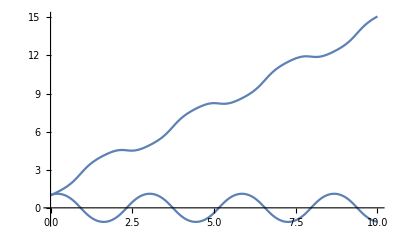

```mathematica
Plot[q /. solution, { t,0,10 } ]
```

```mathematica
eqs //. { θ'[t]-> 0 , Cos[θ[t]]-> 1, Sin[θ[t]]-> θ[t] } // TableForm
```

-(m+M) x''[t]-a m θ''[t]==0
-a m (g θ[t]+x''[t]+a θ''[t])==0

```mathematica
Clear[linearized]
linearized = 
eqs //. { θ'[t]-> 0 , Cos[θ[t]]-> 1, Sin[θ[t]]-> θ[t] }
```

{-(m+M) x''[t]-a m θ''[t]==0,-a m (g θ[t]+x''[t]+a θ''[t])==0}

```mathematica
Eliminate[ linearized, x''[t]]
```

a m M (g θ[t]+a θ''[t])==-a g m^2 θ[t]

```mathematica
Solve[
Eliminate[ linearized, x''[t]] , θ''[t]] // Simplify
```

{{θ''[t]→-(g (m+M) θ[t])/(a M)}}

```mathematica
Coefficient[Simplify[Flatten[Solve[
Eliminate[ linearized, x''[t]] , θ''[t]]][[1,2]]], θ[t]]
```

-(g (m+M))/(a M)

```mathematica
Exit[]
Quit[]
```